{{ψ1→InterpolatingFunction[{{0., 15.}, {…, -25., 25., …}}, <>],ψ2→InterpolatingFunction[{{0., 15.}, {…, -25., 25., …}}, <>]}}

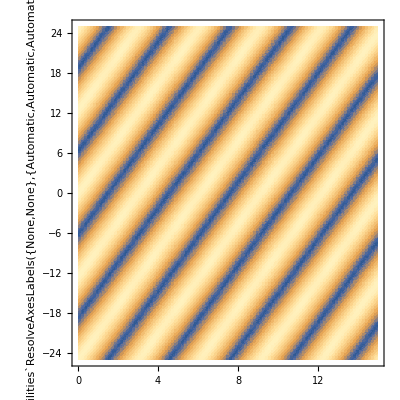

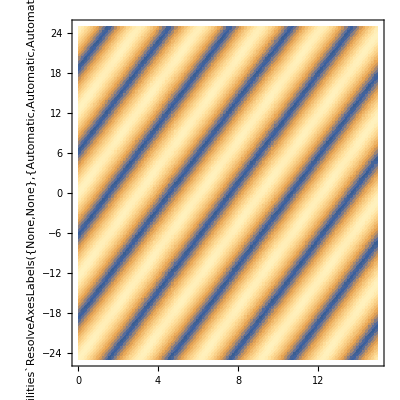

```mathematica
ћ=1;
m=1;
c=1;
X=25;
p=2π/X;
ψ10=ⅇ^(I p x)/(√X);
ψ20=(p c ⅇ^(I p x))/(√X(√(p^2 c^2+m^2 c^4)+m c^2));

s=NDSolve[{I*ћ*D[ψ1[t,x],t]==-I*ћ*c*D[ψ2[t,x],x]+m*c^2*ψ1[t,x],I*ћ*D[ψ2[t,x],t]==-I*ћ*c*D[ψ1[t,x],x]-m*c^2*ψ2[t,x],ψ1[t,-X]==ψ1[t,X],ψ1[0,x]==ψ10,ψ2[t,-X]==ψ2[t,X],ψ2[0,x]==ψ20},{ψ1,ψ2},{t,0,15},{x,-X,X}]

DensityPlot[Abs[Re[ψ1[t,x]]]/.s,{t,0,15},{x,-X,X},PlotPoints->100]
DensityPlot[Abs[Re[ψ2[t,x]]]/.s,{t,0,15},{x,-X,X},PlotPoints->100]

Animate[Show[Plot[{Re[ψ1[t,x]]/.s,Im[ψ1[t,x]]/.s},{x,-X,X},PlotRange->{-12/X,12/X},Filling->Axis],BoxRatios->Automatic],{t,0,15},AnimationRate->1, AnimationRunning->False,RefreshRate->60]
Animate[Show[Plot[{Re[ψ2[t,x]]/.s,Im[ψ2[t,x]]/.s},{x,-X,X},PlotRange->{-12/X,12/X},Filling->Axis],BoxRatios->Automatic],{t,0,15},AnimationRate->1, AnimationRunning->False,RefreshRate->60]
Animate[Show[Plot[{Re[ψ1[t,x]]/.s,Im[ψ1[t,x]]/.s,Re[ψ2[t,x]]/.s,Im[ψ2[t,x]]/.s},{x,-X,X},PlotRange->{-12/X,12/X},Filling->Axis],BoxRatios->Automatic],{t,0,15},AnimationRate->1, AnimationRunning->False,RefreshRate->60]
```